```mathematica
D[ArcCos[z/Sqrt[x^2+y^2 + z^2]],z]//FullSimplify
```

-(√((x^2+y^2)/(x^2+y^2+z^2)))/(√(x^2+y^2+z^2))

calcula el laplaciano de f(r)Ylm(θ,ϕ) y luego dividido entre Ylm

```mathematica
Laplacian[f[r]SphericalHarmonicY[0,0,θ,ϕ],{r,θ,ϕ},"Spherical"]/SphericalHarmonicY[0,0,θ,ϕ] //FullSimplify
```

(2 f'[r])/r+f''[r]

```mathematica
Laplacian[f[r]SphericalHarmonicY[1,0,θ,ϕ],{r,θ,ϕ},"Spherical"]/SphericalHarmonicY[1,0,θ,ϕ] //FullSimplify
```

(2 (-f[r]+r f'[r]))/r^2+f''[r]

```mathematica
Laplacian[f[r]SphericalHarmonicY[2,2,θ,ϕ],{r,θ,ϕ},"Spherical"]/SphericalHarmonicY[2,2,θ,ϕ] //FullSimplify
```

(2 (-3 f[r]+r f'[r]))/r^2+f''[r]

```mathematica
For[i = 0 , i<5,i++,Print["l=",i,", m=0: ",SphericalHarmonicY[i,0,θ,ϕ]]]//FullSimplify
```

l=0, m=0: 1/(2 √π)

l=1, m=0: 1/2 √(3/π) Cos[θ]

l=2, m=0: 1/4 √(5/π) (-1+3 Cos[θ]^2)

l=3, m=0: 1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3)

l=4, m=0: (3 (3-30 Cos[θ]^2+35 Cos[θ]^4))/(16 √π)

```mathematica
SphericalHarmonicY[2,0,θ,ϕ]
```

1/4 √(5/π) (-1+3 Cos[θ]^2)

```mathematica
With[{l= 3, m=-2},SphericalPlot3D[SphericalHarmonicY[l,m,θ,ϕ]*Conjugate[SphericalHarmonicY[l,m,θ,ϕ]],{θ,0,Pi},{ϕ,0,2Pi}]]
```

-Graphics3D-

```mathematica
With[{l= 1, m=0},DensityPlot3D[SphericalHarmonicY[l,m,ArcCos[z/Sqrt[x^2 + y^2 + z^2]],ArcTan[z,y]]*Conjugate[SphericalHarmonicY[l,m,ArcCos[z/Sqrt[x^2 + y^2 + z^2]],ArcTan[z,y]]],{x,y,z}∈Ball[{0,0,0},1],PlotLegends->Automatic]]
```

-Graphics3D-

```mathematica
With[{l= 2, m=0},DensityPlot3D[SphericalHarmonicY[l,m,ArcCos[z/Sqrt[x^2 + y^2 + z^2]],ArcTan[z,y]]*Conjugate[SphericalHarmonicY[l,m,ArcCos[z/Sqrt[x^2 + y^2 + z^2]],ArcTan[z,y]]],{x,y,z}∈Ball[{0,0,0},1],PlotLegends->Automatic]]
```

-Graphics3D-

Calcula los coeficientes de Gaunt  (G_(m1 m2 m))^(l1 l2 l), la integral de la multiplicacion de 3 armonicos esfericos

```mathematica
Gaunt[l1_,l2_,l_, m1_,m2_,m_]:=Integrate[SphericalHarmonicY[l1,m1,θ,ϕ]*SphericalHarmonicY[l2,m2,θ,ϕ]*Conjugate[SphericalHarmonicY[l,m,θ,ϕ]]Sin[θ],{θ,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
Gaunt[2,1,1,0,0,0]
```

1/(√(5 π))

```mathematica
Gaunt[1,1,0,0,0,0]
```

1/(2 √π)

```mathematica
Gaunt[1,1,2,0,0,0]
```

1/(√(5 π))

Calcular el modulo al cuadrado de harmonicos esfericos

```mathematica
Simplify[With[{l=2, m=0},SphericalHarmonicY[l,m,θ,ϕ]*Conjugate[SphericalHarmonicY[l,m,θ,ϕ]]],Assumptions->{Element[θ,Reals],Element[ϕ,Reals]}]
```

(5 (1+3 Cos[2 θ])^2)/(64 π)

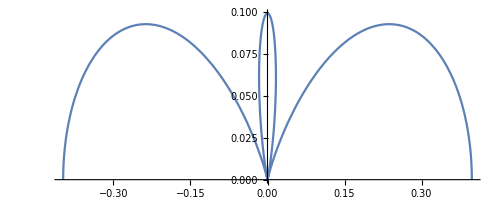

```mathematica
PolarPlot[(5 (1+3 Cos[2 θ])^2)/(64 π),{θ,0,π}]
```

Calcular integral de multiplicacion de 2 harmonicos esfericos uno real y uno complejo conjugado

```mathematica
With[{l1= 2,m1=0 , l2=2,m2= 0},Integrate[SphericalHarmonicY[l1,m1,θ,ϕ]*Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]]Sin[θ],{θ,0,Pi},{ϕ,0,2Pi}]]
```

1

```mathematica
Simplify[With[{l=3},Sum[SphericalHarmonicY[l,m,θ,ϕ]*Conjugate[SphericalHarmonicY[l,m,θ,ϕ]], {m, -l, l}]],Assumptions->{Element[θ,Reals],Element[ϕ,Reals]}]
```

7/(4 π)

```mathematica
(2l+1)/(4 π)
```